# Taylor polynomial demonstration

For PHYS/MATH 4325, Texas Tech
Prof. Katharine Long

### Set up a function to plot Taylor polynomials of several orders about an expansion point

Find the Taylor polynomial of degree n for f(x) about the point a.

```mathematica
Subscript[T, n_][f_,a_,x_]:=Normal[Series[f, {x, a, n}]]
```

Plot f(x) and the Taylor polynomials about a point a, on the interval [xMin,xMax].

```mathematica
TaylorPlot[f_,a_,n_,{xMin_,xMax_},opts: OptionsPattern[]]:=Plot[
Evaluate@Join[{f}, Table[Subscript[T, k][f,a,x],{k,1,n}]],
{x, xMin, xMax},
PlotLegends->Join[{f}, Table[StringForm["Taylor n=``", k], {k, 1, n}]],
PlotStyle->Join[{Thickness[0.01]},Table[Automatic,{n}]],
FrameLabel->{"x", "f(x)", StringForm["`` and Taylor polynomials about a=``",f,a]},
Epilog->{PointSize[0.02],Point[{a, f /. x->a}]},
Evaluate[FilterRules[{opts}, Options[Plot]]]
]
```

An example plot.

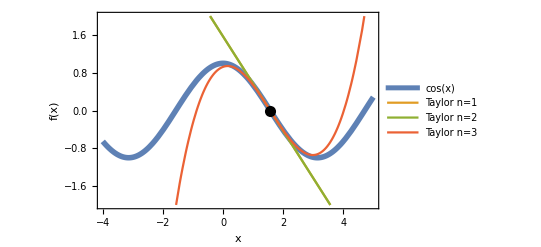

```mathematica
TaylorPlot[Cos[x],Pi/2,3,{-4,5},PlotRange->{-2,2}]
```

Make an interactive demo where the expansion point a and the order n can be varied.

```mathematica
TaylorDemo[f_,{xMin_,xMax_},opts: OptionsPattern[]]:=Manipulate[
TaylorPlot[f, a,n,{xMin,xMax},opts],
{{a,(xMin+xMax)/2},xMin,xMax,Appearance->"Labeled"},
{{n,3},1,6,1,Appearance->"Labeled"}]
```

## Run the demo

```mathematica
TaylorDemo[Cos[x],{-4,4},PlotRange->{-2,2}]
```